{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{0,0,1,0,2,1,5,3,8,12,8,11,5,5,0,0,0,0,0,0}

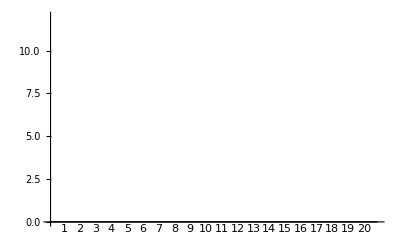

```mathematica
types = Table[i,{i,20}]
fitnesses=Table[RandomVariate[PoissonDistribution[10*Exp[(-(i-10)^2)/10]]],{i,20}]
BarChart[fitnesses,ChartLabels->types,ChartStyle->White]
```